```mathematica
(*Coment*)
```

Text cell

Creating functions with :=

```mathematica
f[x_] := x^2 + 1
```

```mathematica
f[0]
```

1

```mathematica
f[2]
```

5

5

lists

```mathematica
g={1,2,3}
```

{1,2,3}

Accessing list elements

```mathematica
g{2}
```

Thread::tdlen: Objects of unequal length in {1,2,3} {2} cannot be combined.

```mathematica
{{□}, {}}
```

{2} {1,2,3}

```mathematica
% 99 (*access yo lsdy *)
```

{2} {1,2,3}

```mathematica
3+2
```

5

```mathematica
β
```

β

## Defining functions

```mathematica
f[x_] := Sin[x]
```

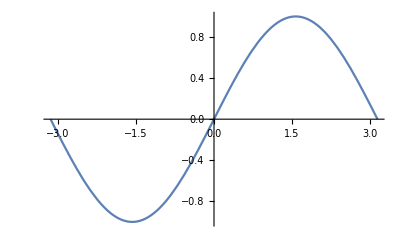

```mathematica
Plot[f[x], {x, -Pi, Pi}]
```

# Lists

```mathematica
A = {1,2,3,4};
```

```mathematica
A[[2]]
```

2

```mathematica
Teste = Table[RandomReal[{0,1}],{i,1,5}]Table[RandomReal[{0,1}],{i,1,5}]
```

{0.55452,0.0706441,0.113156,0.291925,0.0805673}

```mathematica
First[Teste] (*return first item from list*)
```

0.55452

```mathematica
Last[Teste]
```

0.0805673

```mathematica
Total[Teste] (*Sum of everything*)
```

1.11081

```mathematica
Sum[Teste[[i]], {i, 1, 3}] (*partial sum*)
```

0.73832

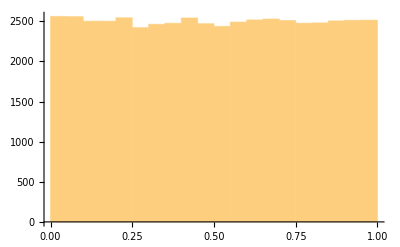

```mathematica
mylist3=Table[RandomReal[],{50000}];
Histogram[mylist3]
```